```mathematica
2-2
```

0

# Random Walks on a Hexagonal Lattice

Nicholas Wheeler
1 December 2011

### Introduction

This work is motivated by my 2nd conversation with Sina Zeytinoglu (whose previous visit motivated me to write "Iteration Techniques" (23 November 2011)). Here is a hexagonal lattice:

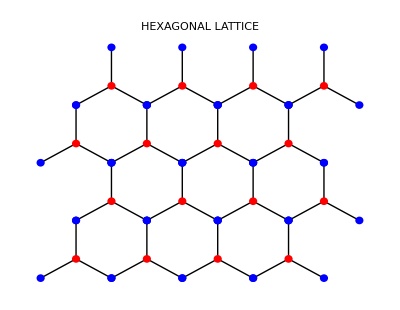

Notice that this is what I have been motivated elsewhere to call a "blinking" design: the node on which the walker stands changes color with each step.

The following vectors describe the steps (of unit length) available to a walker who stands on ●

```mathematica
Subscript[R, 1]={Cos[π/2],Sin[π/2]};
Subscript[R, 2]={Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]};
Subscript[R, 3]={Cos[π/2-8(2π)/12],Sin[π/2-8(2π)/12]};
```

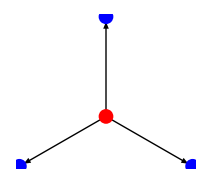

```mathematica
RedOptions=Graphics[{{Red, PointSize[0.05],Point[{0,0}]},
{Blue, PointSize[0.05],Point[Subscript[R, 1]]},
{Blue, PointSize[0.05],Point[Subscript[R, 2]]},
{Blue, PointSize[0.05],Point[Subscript[R, 3]]},
{Arrow[{{0,0},Subscript[R, 1]},.05]},
{Arrow[{{0,0},Subscript[R, 2]},.05]},
{Arrow[{{0,0},Subscript[R, 3]},.05]}}]
```

while these vectors—the negatives of the preceding vectors—describe the unit steps available to a walker who stands momentarily on ●:

```mathematica
Subscript[B, 1]=-Subscript[R, 1];
Subscript[B, 2]=-Subscript[R, 2];
Subscript[B, 3]=-Subscript[R, 3];
```

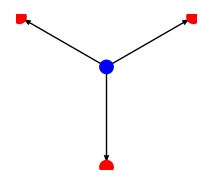

```mathematica
BlueOptions=Graphics[{{Blue, PointSize[0.05],Point[{0,0}]},
{Red, PointSize[0.05],Point[Subscript[B, 1]]},
{Red, PointSize[0.05],Point[Subscript[B, 2]]},
{Red, PointSize[0.05],Point[Subscript[B, 3]]},
{Arrow[{{0,0},Subscript[B, 1]},.05]},
{Arrow[{{0,0},Subscript[B, 2]},.05]},
{Arrow[{{0,0},Subscript[B, 3]},.05]}}]
```

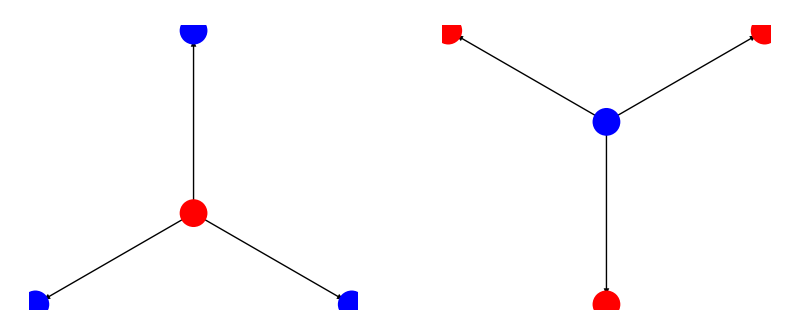

```mathematica
GraphicsArray[{RedOptions, BlueOptions}]
```

### "By hand" construction of a 30-step hexagonal walk

The following multiple command serves to construct 30-step hexagonal walks "by hand":

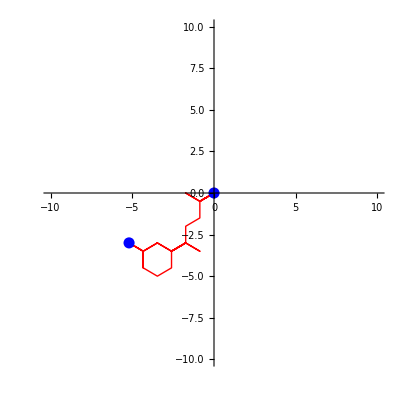

```mathematica
Subscript[S, 1]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 2]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 3]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 4]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 5]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 6]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 7]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 8]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 9]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 10]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 11]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 12]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 13]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 14]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 15]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 16]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 17]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 18]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 19]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 20]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 21]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 22]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 23]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 24]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 25]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 26]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 27]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 28]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
Subscript[S, 29]=RandomChoice[{Subscript[R, 1],Subscript[R, 2],Subscript[R, 3]}];
Subscript[S, 30]=RandomChoice[{Subscript[B, 1],Subscript[B, 2],Subscript[B, 3]}];
SuccessivePositions=Table[Subscript[P, k]=∑_(j=1)^k Subscript[S, j],{k,1,30}];
HexagonalWalk=Prepend[SuccessivePositions,{0,0}];

Walk30=ListLinePlot[HexagonalWalk,AspectRatio->Automatic, AxesOrigin->{0,0}, PlotRange->{{-10,10},{-10,10}}, PlotStyle->{Thick, Red}];

EndPoints30=Graphics[{{Blue, PointSize[0.02],Point[{0,0}]},
{Blue, PointSize[0.02],Point[Last[HexagonalWalk]]}}];

Show[{Walk30,EndPoints30}]
```

Many repetitions later, I am surprised by the frequency with which the walker doubles back, retraces previous steps.

### Automating the construction of such walks

I can't get the Nest command to construct alternating RBRBRBRB sequences, so adopt a relatively clumsy procedure of which I provide first a sketch:

```mathematica
A=Table[Transpose[{{RandomChoice[{R1, R2, R3}],RandomChoice[{B1, B2, B3}]}}],{k,1,10}]

B=Table[MatrixPower[({{0, 1}, {1, 0}}),k].A⟦k⟧,{k,1,10}]

Steps=Table[Flatten[B⟦k⟧⟦1⟧]⟦1⟧,{k,1,10}]
```

{{{R3},{B3}},{{R3},{B2}},{{R2},{B2}},{{R1},{B3}},{{R1},{B3}},{{R3},{B2}},{{R3},{B1}},{{R3},{B1}},{{R2},{B1}},{{R2},{B2}}}

{{{B3},{R3}},{{R3},{B2}},{{B2},{R2}},{{R1},{B3}},{{B3},{R1}},{{R3},{B2}},{{B1},{R3}},{{R3},{B1}},{{B1},{R2}},{{R2},{B2}}}

{B3,R3,B2,R1,B3,R3,B1,R3,B1,R2}

In the context at hand the objects R1, R2, ...,  B3 are 2-vectors. I find that  Mathematica objects to subscripted notation in this context, so I renotate my vectors:

```mathematica
R1={Cos[π/2],Sin[π/2]};
R2={Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]};
R3={Cos[π/2-8(2π)/12],Sin[π/2-8(2π)/12]};
B1=-R1;
B2=-R2;
B3=-R3;
```

Step 1 of the procedure sketched above produces

```mathematica
A=Table[Transpose[{{RandomChoice[{R1, R2, R3}],RandomChoice[{B1, B2, B3}]}}],{k,1,10}]
```

{{{{-(√3)/2,-1/2}},{{(√3)/2,1/2}}},{{{0,1}},{{0,-1}}},{{{0,1}},{{(√3)/2,1/2}}},{{{(√3)/2,-1/2}},{{-(√3)/2,1/2}}},{{{0,1}},{{-(√3)/2,1/2}}},{{{(√3)/2,-1/2}},{{-(√3)/2,1/2}}},{{{(√3)/2,-1/2}},{{0,-1}}},{{{0,1}},{{0,-1}}},{{{(√3)/2,-1/2}},{{-(√3)/2,1/2}}},{{{(√3)/2,-1/2}},{{0,-1}}}}

```mathematica
A⟦1⟧
```

{{{-(√3)/2,-1/2}},{{(√3)/2,1/2}}}

The matrix (0 | 1
1 | 0)serves still to reverse those vectors

```mathematica
({{0, 1}, {1, 0}}).%
```

{{{(√3)/2,1/2}},{{-(√3)/2,-1/2}}}

so we construct

```mathematica
B=Table[MatrixPower[({{0, 1}, {1, 0}}),k].A⟦k⟧,{k,1,10}]
```

{{{{(√3)/2,1/2}},{{-(√3)/2,-1/2}}},{{{0,1}},{{0,-1}}},{{{(√3)/2,1/2}},{{0,1}}},{{{(√3)/2,-1/2}},{{-(√3)/2,1/2}}},{{{-(√3)/2,1/2}},{{0,1}}},{{{(√3)/2,-1/2}},{{-(√3)/2,1/2}}},{{{0,-1}},{{(√3)/2,-1/2}}},{{{0,1}},{{0,-1}}},{{{-(√3)/2,1/2}},{{(√3)/2,-1/2}}},{{{(√3)/2,-1/2}},{{0,-1}}}}

Commands such as these serve to extract the leading member of each vector pair:

```mathematica
B⟦1⟧⟦1⟧⟦1⟧
B⟦2⟧⟦1⟧⟦1⟧
B⟦3⟧⟦1⟧⟦1⟧
```

{(√3)/2,1/2}

{0,1}

{(√3)/2,1/2}

We do so, and prepend the zero vector {0,0} so that our walks begin at the origin. We arrive thus as this set of random alternating BRBRBRB steps

```mathematica
Steps=Prepend[Table[B⟦k⟧⟦1⟧⟦1⟧,{k,1,10}],{0,0}]
```

{{0,0},{(√3)/2,1/2},{0,1},{(√3)/2,1/2},{(√3)/2,-1/2},{-(√3)/2,1/2},{(√3)/2,-1/2},{0,-1},{0,1},{-(√3)/2,1/2},{(√3)/2,-1/2}}

which we link together to build up a 10-step walk:

```mathematica
Walk=Table[∑_(j=1)^k Steps⟦j⟧,{k,1,11}]
```

{{0,0},{(√3)/2,1/2},{(√3)/2,3/2},{√3,2},{(3 √3)/2,3/2},{√3,2},{(3 √3)/2,3/2},{(3 √3)/2,1/2},{(3 √3)/2,3/2},{√3,2},{(3 √3)/2,3/2}}

The walk thus generated looks like this:

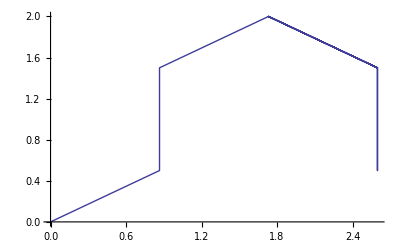

```mathematica
ListLinePlot[Walk]
```

We now consolidate those commands to produce at random a 200-step hexagonal walk with a single composite command:

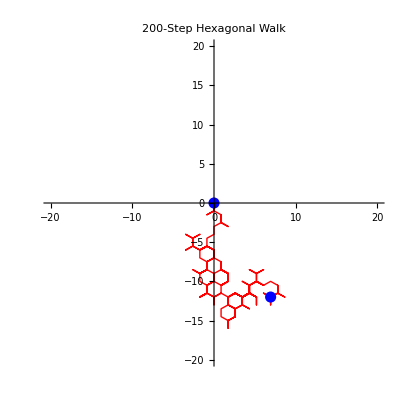

```mathematica
A200=Table[Transpose[{{RandomChoice[{R1, R2, R3}],RandomChoice[{B1, B2, B3}]}}],{k,1,200}];

B200=Table[MatrixPower[({{0, 1}, {1, 0}}),k].A200⟦k⟧,{k,1,200}];

Steps200=Prepend[Table[B200⟦k⟧⟦1⟧⟦1⟧,{k,1,200}],{0,0}];

Walk200=Table[∑_(j=1)^k Steps200⟦j⟧,{k,1,201}];

HexagonalWalk200=ListLinePlot[Walk200,AspectRatio->Automatic, AxesOrigin->{0,0}, PlotRange->{{-20,20},{-20,20}}, PlotStyle->{Thick, Red}];

EndPoints200=Graphics[{{Blue, PointSize[0.02],Point[{0,0}]},
{Blue, PointSize[0.02],Point[Last[Walk200]]}}];

Show[{HexagonalWalk200,EndPoints200},PlotLabel->"200-Step Hexagonal Walk"]
```